b √(1-5/(6+6 b))

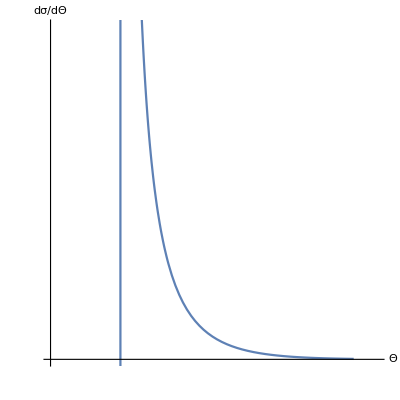

```mathematica
s=b*√(1-5/(6+6b))
ParametricPlot[{Pi-NIntegrate[(2*b*√(1-5/(6+6b)))/(r^2*√(1-5/(6+6r)-(b^2*(1-5/(6+6b)))/r^2)),{r,b+0.005,Infinity}],s/(Sin[NIntegrate[(2*b*√(1-5/(6+6b)))/(r^2*√(1-5/(6+6r)-(b^2*(1-5/(6+6b)))/r^2)),{r,b+0.005,Infinity}]]*((6+6b)/(b*((5b)/(2+2b)+1+6b))*(2*√(1+6b))/(√(0.005*((5*b^2)/(1+b)+12*b^2+2b)))-NIntegrate[(1+6r)/((3+3r)*r^2*(1-5/(6+6r)-(b^2*(1-5/(6+6b)))/r^2)^1.5),{r,b+0.005,Infinity}]))},{b,0.2588,1.2588},AxesLabel->{Θ,dσ/dΘ},PlotRange->{{0.4,0.9},{0,0.5}},Ticks->None]
```